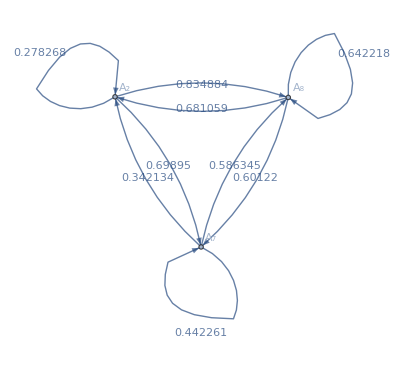

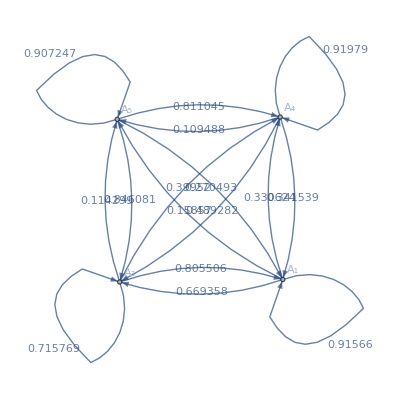

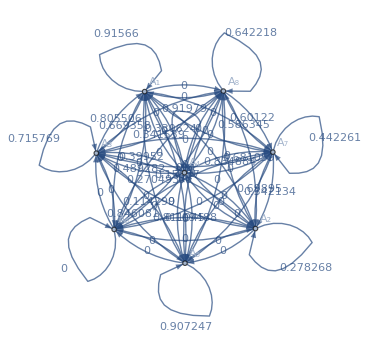

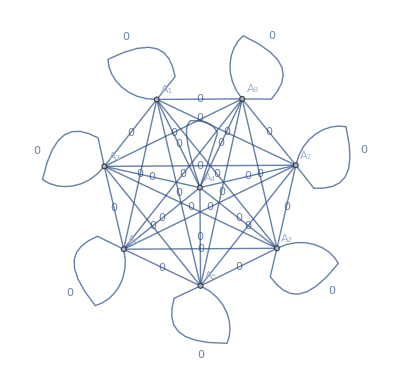

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of FullSimplify::fas will be suppressed during this calculation.

1.08645

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of FullSimplify::fas will be suppressed during this calculation.

1.30985

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of FullSimplify::fas will be suppressed during this calculation.

1.30985

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of FullSimplify::fas will be suppressed during this calculation.

0

```mathematica
n1=3;
n2=4;
Vertices=Table[Subscript[A, i], {i, 1, Max[n1, n2]+4}];
chain1=(*#/Total[#]&/@*)Table[RandomReal[], {i, 1, n1}, {j, 1, n1}];
chain2=(*#/Total[#]&/@*)Table[RandomReal[], {i, 1, n2}, {j, 1, n2}];
ag1=WeightedAdjacencyGraph[RandomSample[Vertices, n1], chain1, VertexLabels->"Name", EdgeLabels->"EdgeWeight"]
ag2=WeightedAdjacencyGraph[RandomSample[Vertices, n2], chain2, VertexLabels->"Name", EdgeLabels->"EdgeWeight"]
chain1=ExpandAndReshape[ag1, Vertices];
chain2=ExpandAndReshape[ag2, Vertices];

unionchain=WeightedUnionAdjacencyMatrix[chain1, chain2];
intersectionchain=WeightedIntersectionAdjacencyMatrix[chain1, chain2];
WeightedAdjacencyGraph[Vertices, unionchain, VertexLabels->"Name", EdgeLabels->"EdgeWeight"]
WeightedAdjacencyGraph[Vertices, intersectionchain, VertexLabels->"Name", EdgeLabels->"EdgeWeight"]

chain1//StationaryVector//NormalizeVector//ProcessEntropy
chain2//StationaryVector//NormalizeVector//ProcessEntropy
unionchain//StationaryVector//NormalizeVector//ProcessEntropy
intersectionchain//StationaryVector//NormalizeVector//ProcessEntropy
```

```mathematica
chain1//NormalizeRows
chain2//NormalizeRows//StationaryVector//ProcessEntropy
unionchain//NormalizeRows//StationaryVector//ProcessEntropy
intersectionchain//NormalizeRows//StationaryVector//ProcessEntropy
```

{{0.0335267,0.,0.,0.411626,0.,0.,0.,0.554847},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.552185,0.,0.,0.273872,0.,0.,0.,0.173943},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.378053,0.,0.,0.26056,0.,0.,0.,0.361388}}

1.32849

1.5288

0.690685

```mathematica
chain1//NormalizeRows
```

{{0.0335267,0.,0.,0.411626,0.,0.,0.,0.554847},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.552185,0.,0.,0.273872,0.,0.,0.,0.173943},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.378053,0.,0.,0.26056,0.,0.,0.,0.361388}}

```mathematica
chain1
```

{{0.0220444,0,0,0.270651,0,0,0,0.364821},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.953368,0,0,0.47285,0,0,0,0.300318},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.649159,0,0,0.44741,0,0,0,0.620543}}

```mathematica
{{a, b}, {c, d}}//NormalizeRows//StationaryVector//ProcessEntropy//FullSimplifyForPositiveReals
```

-((a+b) c Log[((a+b) c)/(a c+b (2 c+d))]+b (c+d) Log[(b (c+d))/(a c+b (2 c+d))])/(a c+b (2 c+d))